# MF IN FINTECH

谢泽健

11810105

HW5

2019.7.27

Q.1 Which of these are posets?

c.

Q.2 Answer these questions for the partial order represented by this Hasse diagram.

a.

l,m

b.

a,b,c,

c.

No

d.

No

e.

k,l,m

f.

k

g.

No exist

h.

No exist

Q.3 Let G be a simple graph with n vertices.

a.

For every w vertices, there can be an edges:

|E|_max=(n
2)=(n(n-1))/2

b.

Suppose the edges of G is {v_0,v_1},{v_(1,)v_2},...{v_(n-1),v_n}, there is n-1 edges.

Then we prove a connected have no less than n-1 edges.

For n = 1 there is nothing to prove.

Now assume the inductive hypothesis, and let G be a connected graph with n + 1 vertices and fewer than n edges, where n ≥ 1. Since the sum of the degrees of the vertices of G is

2|E|≤2n≤2(n+1)

Therefore some vertex has degree less than 2. Since G is connected, this vertex is not isolated, so it must have degree 1. Remove this vertex and its edge. Clearly the result is still connected, and it has n vertices and fewer than n − 1 edges, contradicting the inductive hypothesis. Therefore the statement holds for G, and the proof is complete.

c.

If G is not connected, it has at least two connected subgraph, assume G_1 has k vertices and G_2 has n-k vertices, because for v_0∈V_1

deg(v_0)≥(n-1)/2

hence

k≥1+(n-1)/2=(n+1)/2

for same reason

n-k≥(n+1)/2

contradicting

n-k≤n-(n+1)/2=(n-1)/2

Hence G must be connected.

Q.4 Let n ≥ 5 be an integer. Consider the graph Gn whose vertices are the sets {a, b}, where a, b ∈ {1, . . . , n} and a 6= b, and whose adjacency rule is disjointness, that is, {a, b} is adjacent to {a
a.

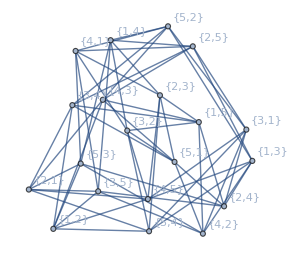

b.

For each vertex, the number of vertex it connected is

2×(n-2
2)=(n-2)(n-3)

Q.5 Let G = (V, E)s be a graph on n vertices. Construct a new

a.

Suppose the edges in G which connect v_i and v_j is {i,j} in G'

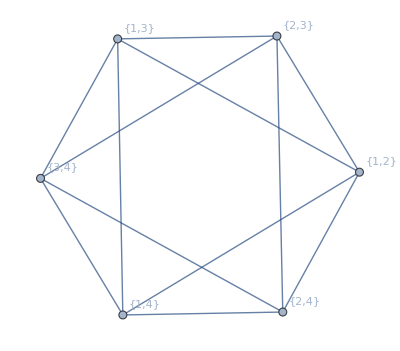

b.

|E'|=∑_(v∈V) deg(v)

Q.6 Let G be a connected graph, with the vertex set V . The distance between two vertices u and v, denoted by dist(u, v), is defined as the minimal length of a path from u to v. Show that dist(u, v) is a metric, i.e., the following properties hold for any u, v, w ∈ V :

Suppose the path from u to v is

u,w_1,w_2,...v

If dist(u,v)=0 and u≠v, there is no exist a path, hence

dist(u,v)⇒u=v

If u=v, the path is

u,u

hence

u=v⇒dist(u,v)

The path from u to v also can be written as the path from v to u:

v,...,w_2,w_1,u

that is, for every path p from u to v, there exist p' from v to u

Length(p)=Length(p')

hence their minimal length is equal:

dist(u,v)=dist(v,u)

The path from u to w and the path from w to v can construct a path from u to v. However dist(u,v) has the minimal length in all the path from u to v:

dist(u,v)≤dist(u,w)+dist(w,v)

Q.7 Show that if G is bipartite simple graph with v vertices and e edges, then e ≤ v^2/4

Suppose the two subset of V is V_1 and V_2, and assume |V_1|=k, we know that

e≤edges number of K_(k,v-k)=k(v-k)

Note

k(v-k)≤v^2/4

Hence

e≤v^2/4

Q.8
(a) What is the sum of the entries in a row of the adjacency matrix for an undirected graph? For a directed graph?
(b) What is the sum of the entries in a column of the adjacency matrix for an undirected graph? For a directed graph?

a

For undirected graph, the sum of the entries in ith row is deg(v_i) while for directed graph is deg^-(v_i)

b.

For undirected graph, the sum of the entries in ith column is deg(v_i) while for directed graph is deg^+(v_i)

Q.9 Show that isomorphism of simple graphs is an equivalence relation.

isomorphism is reflexive:

Let

f(v)=v

Then G and G are isomorphism.

isomorphism is symmetric:

If G and G' are isomorphism, there exist reversible function

f:V→V'

Let

f^-1:V'→V

Then G' and G are isomorphism.

isomorphism is transitive:

If

G isomorphism G',G' isomorphism G''

There exist

f:G→G',g:G'→G''

Then f∘g let G isomorphism G''

Q.10 Show that every connected graph with n vertices has at least n − 1 edges

For n = 1 there is nothing to prove.

Now assume the inductive hypothesis, and let G be a connected graph with n + 1 vertices and fewer than n edges, where n ≥ 1. Since the sum of the degrees of the vertices of G is

2|E|≤2n≤2(n+1)

Therefore some vertex has degree less than 2. Since G is connected, this vertex is not isolated, so it must have degree 1. Remove this vertex and its edge. Clearly the result is still connected, and it has n vertices and fewer than n − 1 edges, contradicting the inductive hypothesis. Therefore the statement holds for G, and the proof is complete.

Q.11 Explain how to find a path with the least number of edges between two vertices in an undirected graph by considering it as a shortest path problem in a weighted graph.

Suppose G=(V,E), where V=v_0,v_1,... v_n and the for every vertex pair

w(v_i,v_j)=Piecewise[{{weight, {v_i,v_j} is an edge}, {∞, otherwise}}]

Then find the shortest path from v_0 to v_n:

```mathematica
For i In range(n):
		L(Subscript[v, i])=∞
	L(Subscript[v, 0])=0
	S=∅
	While Subscript[v, n]∉S:
		u=Min[V-S,key=lambda v:L(v)]
		S=S.append(u)
		For j In V-S:
			If L(u)+w(u,v)<L(v):
				L(v)=L(u)+w(u,v)
	Return L(Subscript[v, n])
```

Q.12 Which of the these nonplanar graphs have the property that the removal of any vertex and all edges incident with that vertex produces a palnar graph?

a,c